# Game theoretic approach of Hypothesis testing

## Data focused

```mathematica
p[k_][pA_][Ν_]:=Binomial[Ν, k] pA^k(1-pA)^(Ν-k)
ΔI[p_,pʹ_]:=-(p Log[pʹ/p]+(1-p) Log[(1-pʹ)/(1-p)])
pʹ[l_][pA_,pB_][Ν_][P_]:=(pA P p[l][pA][Ν]+pB (1-P)p[l][pB][Ν])/(P p[l][pA][Ν]+(1-P)p[l][pB][Ν])
Δ[P_][pA_,pB_][Ν_]:=P (∑_(k=0)^Ν p[k][pA][Ν] ΔI[pA,pʹ[k][pA,pB][Ν][P]])+(1-P) (∑_(k=0)^Ν p[k][pB][Ν] ΔI[pB,pʹ[k][pA,pB][Ν][P]])
P eq[pA_,pB_][Ν_]:=P/.FindMaximum[{Δ[P][pA,pB][Ν],P<1,P>0},{P,1/2}]⟦2⟧
```

```mathematica
Manipulate[
"pA="<>ToString[pA]<>"\n"<>
"pB="<>ToString[pB]<>"\n"<>
"N="<>ToString[Ν]<>"\n"<>"\n"<>
"P^*="<>ToString[P eq[pA,pB][Ν]],
{{pA,0.5},0,1},
{{pB,0.7},0,1},
{{Ν,8},0,30,1}]
```

```mathematica
Manipulate[
"pA="<>ToString[pA]<>"\n"<>
"pB="<>ToString[pB]<>"\n"<>
"k="<>ToString[k]<>"\n"<>
"N="<>ToString[Ν]<>"\n"<>"\n"<>
"pʹ="<>ToString[pʹ[k][pA,pB][Ν][P eq[pA,pB][Ν]]],
{{pA,0.5},0,1},
{{pB,0.7},0,1},
{{Ν,8},0,30,1},
{k,0,Ν,1}]
```

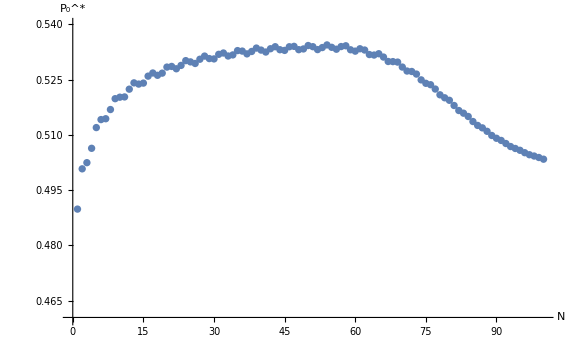

```mathematica
With[
{pA=1/2,pB=9/10},
ListPlot[Table[P eq[pA,pB][Ν],{Ν,1,100}],
PlotRange->{0.46,0.54},AxesLabel->{"N","P_0^*"},ImageSize->Large]
]
```